```mathematica
f1=(1-2/R)^(-1/2);
f2=(1-3/R);
```

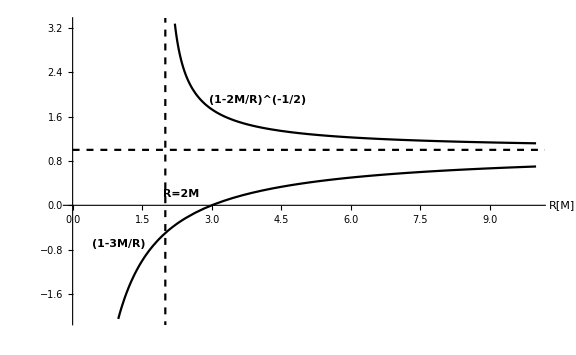

```mathematica
pl1=Plot[{(1-2/R)^(-1/2),(1-3/R)},{R,0,10},PlotStyle->Black,AxesLabel->{"R[M]"}];
texts1=Graphics[{
Text[Style["(1-2M/R)^(-1/2)",11,Bold],{4.,1.9},FormatType->TraditionalForm],
Text[Style["R=2M",11,Bold],{2.35,0.2},FormatType->TraditionalForm],
Text[Style["(1-3M/R)",11,Bold],{1.,-0.7},FormatType->TraditionalForm]
}];
ppp=ParametricPlot[{2,t},{t,-4,4},PlotStyle->{Black,Dashed}];
ppp2=ParametricPlot[{t,1},{t,0,12},PlotStyle->{Black,Dashed}];
Show[pl1,ppp,ppp2,texts1,ImageSize->Large]
```